# Detexon

```mathematica
Quit[]
```

## Import Test Data

```mathematica
ds=Import@FileNameJoin[{NotebookDirectory[],"data","test_set.mx"}];
```

## Import Net

```mathematica
tNet=Import["~/Downloads/latest_ec2/checkpoints_y2018_m7_d6_h13_s2/net.wlnet"]
```

NetGraph[<>]

#### Net Architecture

NetGraph[<>]

## Visualization Helpers

```mathematica
probabilitiesToClass[probMat_]:=Flatten[Ordering[#,-1]&/@probMat]
randomN[ds_]:=RandomInteger[{1,Length[ds]}];
```

## Randomly Sample Test data and visualize

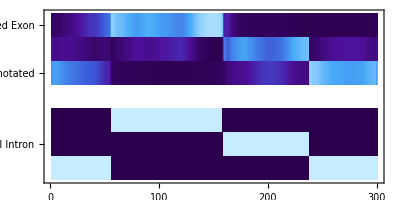

```mathematica
n=randomN[ds];
(*n=6028;*)
s=Normal[ds[n]];
Module[
{
to=Transpose@tNet[s["Input"]],
no=Transpose@Normal[s["Output"]]
},
ap=ArrayPlot[
Join[
to,
{Table[{White,Opacity[0]},300]},
no
],AspectRatio->1/2,
Background->White,
Frame->True,FrameTicks->{
{
{1, "Predicted Exon"},
{2, "Predicted Intron"},
{3, "Predicted Unannotated"},
{5, "Real Exon"},
{6, "Real Intron"},
{7, "Real Unannotated"}
}
,{0, 50, 100, 150, 200, 250, 300}
},
PlotLegends->Placed[Automatic,Bottom],
ColorFunction->"DeepSeaColors"
]
]
```